# Information Geometry of the Weibull Distribution

## Nicholas Wisniewski

```mathematica
Clear[x]
```

```mathematica
a=k;
b=λ;
distribution=PDF[WeibullDistribution[a,b],x];
pdfCoords={a,b};
pdfAssumptions={a>0,b>0};
pdfIntegrationLimits={0,∞};
```

```mathematica
g=FisherMetric[distribution,pdfCoords,pdfAssumptions,pdfIntegrationLimits]
```

{{(6 (-1+EulerGamma)^2+π^2)/(6 k^2),(-1+EulerGamma)/λ},{(-1+EulerGamma)/λ,k^2/λ^2}}

```mathematica
g={{(6 (-1+EulerGamma)^2+π^2)/(6 k^2),(-1+EulerGamma)/λ},{(-1+EulerGamma)/λ,k^2/λ^2}}
```

{{(6 (-1+EulerGamma)^2+π^2)/(6 k^2),(-1+EulerGamma)/λ},{(-1+EulerGamma)/λ,k^2/λ^2}}

```mathematica
Γ=LeviCivitaCoefficients[g,pdfCoords]
```

{{{-(6 (-1+EulerGamma)^2+π^2)/(k π^2),((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ)/(k^3 π^2)},{-(6 (-1+EulerGamma) k)/(π^2 λ),(6 (-1+EulerGamma)^2+π^2)/(k π^2)}},{{-(6 (-1+EulerGamma) k)/(π^2 λ),(6 (-1+EulerGamma)^2+π^2)/(k π^2)},{-(6 k^3)/(π^2 λ^2),-(6 k-6 EulerGamma k+π^2)/(π^2 λ)}}}

```mathematica
Γ={{{-(6 (-1+EulerGamma)^2+π^2)/(k π^2),((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ)/(k^3 π^2)},{-(6 (-1+EulerGamma) k)/(π^2 λ),(6 (-1+EulerGamma)^2+π^2)/(k π^2)}},{{-(6 (-1+EulerGamma) k)/(π^2 λ),(6 (-1+EulerGamma)^2+π^2)/(k π^2)},{-(6 k^3)/(π^2 λ^2),-(6 k-6 EulerGamma k+π^2)/(π^2 λ)}}}
```

{{{-(6 (-1+EulerGamma)^2+π^2)/(k π^2),((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ)/(k^3 π^2)},{-(6 (-1+EulerGamma) k)/(π^2 λ),(6 (-1+EulerGamma)^2+π^2)/(k π^2)}},{{-(6 (-1+EulerGamma) k)/(π^2 λ),(6 (-1+EulerGamma)^2+π^2)/(k π^2)},{-(6 k^3)/(π^2 λ^2),-(6 k-6 EulerGamma k+π^2)/(π^2 λ)}}}

```mathematica
Γα=AlphaCoefficients[distribution,g,pdfCoords,pdfAssumptions,pdfIntegrationLimits]
```

({(k (α-1) 2k)/(2-2 k 1k),((α-1) θ 2k)/(2 k 1k-2)} | {(1-α)/(2 θ-2 k θ 1k),((α-1) 1k)/(2-2 k 1k)}
{(1-α)/(2 θ-2 k θ 1k),((α-1) 1k)/(2-2 k 1k)} | {(k (α-1))/(2 θ^2 (k 1k-1)),(α-2 k (α+1) 1k+3)/(2 θ (k 1k-1))})

```mathematica
Γα/.{α->0}
Γα/.{α->1}
Γα/.{α->-1}
```

({-(k 2k)/(2-2 k 1k),-(θ 2k)/(2 k 1k-2)} | {1/(2 θ-2 k θ 1k),-(1k)/(2-2 k 1k)}
{1/(2 θ-2 k θ 1k),-(1k)/(2-2 k 1k)} | {-k/(2 θ^2 (k 1k-1)),(3-2 k 1k)/(2 θ (k 1k-1))})

({0,0} | {0,0}
{0,0} | {0,(4-4 k 1k)/(2 θ (k 1k-1))})

({-(2 k 2k)/(2-2 k 1k),-(2 θ 2k)/(2 k 1k-2)} | {2/(2 θ-2 k θ 1k),-(2 1k)/(2-2 k 1k)}
{2/(2 θ-2 k θ 1k),-(2 1k)/(2-2 k 1k)} | {-k/(θ^2 (k 1k-1)),1/(θ (k 1k-1))})

```mathematica
Ruplijk=RiemannTensor1[Γ,pdfCoords]
```

{{{{0,(6-6 EulerGamma)/(π^2 λ)},{(6 (-1+EulerGamma))/(π^2 λ),0}},{{0,-(6 k^2)/(π^2 λ^2)},{(6 k^2)/(π^2 λ^2),0}}},{{{0,(6 (-1+EulerGamma)^2+π^2)/(k^2 π^2)},{-(6 (-1+EulerGamma)^2+π^2)/(k^2 π^2),0}},{{0,(6 (-1+EulerGamma))/(π^2 λ)},{(6-6 EulerGamma)/(π^2 λ),0}}}}

```mathematica
Rdownlijk=RiemannTensor2[Γ,g,pdfCoords]
```

{{{{0,0},{0,0}},{{0,-1/λ^2},{1/λ^2,0}}},{{{0,1/λ^2},{-1/λ^2,0}},{{0,0},{0,0}}}}

```mathematica
Rij=RicciTensor[Ruplijk,pdfCoords]
```

{{-(6 (-1+EulerGamma)^2+π^2)/(k^2 π^2),(6-6 EulerGamma)/(π^2 λ)},{(6-6 EulerGamma)/(π^2 λ),-(6 k^2)/(π^2 λ^2)}}

```mathematica
R=ScalarCurvature[Rij,g,pdfCoords]
```

-(12 (6-6 EulerGamma) (-1+EulerGamma))/π^4-(12 (6 (-1+EulerGamma)^2+π^2))/π^4

```mathematica
R//N
```

-1.21585

```mathematica
Solve[R==0,{α}]
```

{{α→-1},{α→1}}

```mathematica
geodesics=EulerLagrangeEquations[Γ,pdfCoords,t]
```

{-1/(k π^2 λ^2)((6 (-1+EulerGamma)^2+π^2) λ^2 k'[t]^2+12 (-1+EulerGamma) k^2 λ k'[t] λ'[t]+6 k^4 λ'[t]^2)+k''[t],1/(k^3 π^2 λ)((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ^2 k'[t]^2+2 k^2 (6 (-1+EulerGamma)^2+π^2) λ k'[t] λ'[t]+k^3 (6 (-1+EulerGamma) k-π^2) λ'[t]^2)+λ''[t]}

```mathematica
{-1/(k π^2 λ^2)((6 (-1+EulerGamma)^2+π^2) λ^2 k'[t]^2+12 (-1+EulerGamma) k^2 λ k'[t] λ'[t]+6 k^4 λ'[t]^2)+k''[t],1/(k^3 π^2 λ)((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ^2 k'[t]^2+2 k^2 (6 (-1+EulerGamma)^2+π^2) λ k'[t] λ'[t]+k^3 (6 (-1+EulerGamma) k-π^2) λ'[t]^2)+λ''[t]}//TraditionalForm
```

{k''(t)-(6 k^4 (λ'(t))^2+(6 (ℽ-1)^2+π^2) λ^2 (k'(t))^2+12 (ℽ-1) λ k^2 k'(t) λ'(t))/(π^2 k λ^2),1/(π^2 k^3 λ)((6 (ℽ-1) k-π^2) k^3 (λ'(t))^2+(ℽ-1) (6 (ℽ-1)^2+π^2) λ^2 (k'(t))^2+2 (6 (ℽ-1)^2+π^2) λ k^2 k'(t) λ'(t))+λ''(t)}

k^(..)=(6 k^4 (λ̇)^2+(6 (ℽ-1)^2+π^2) λ^2 (k̇)^2+12 (ℽ-1) λ k^2 k̇ λ̇)/(π^2 k λ^2)
λ^(..)=-((6 (ℽ-1) k-π^2) k^3 (λ̇)^2+(ℽ-1) (6 (ℽ-1)^2+π^2) λ^2 (k̇)^2+2 (6 (ℽ-1)^2+π^2) λ k^2 k̇ λ̇)/(π^2 k^3 λ)

```mathematica
sol=Table[NDSolve[{-1/(k[t] π^2 λ[t]^2)((6 (-1+EulerGamma)^2+π^2) λ[t]^2 k'[t]^2+12 (-1+EulerGamma) k[t]^2 λ[t] k'[t] λ'[t]+6 k[t]^4 λ'[t]^2)+k''[t]==0,1/(k[t]^3 π^2 λ[t])((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ[t]^2 k'[t]^2+2 k[t]^2 (6 (-1+EulerGamma)^2+π^2) λ[t] k'[t] λ'[t]+k[t]^3 (6 (-1+EulerGamma) k[t]-π^2) λ'[t]^2)+λ''[t]==0,k[0]==1,λ[0]==i,k'[0]==1,λ'[0]==1},{k,λ},{t,-10,10}],{i,1,6}]
```

{{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}}}

```mathematica
sol[[2,1]]
```

{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}

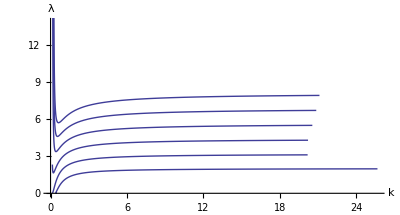

```mathematica
pl1=ParametricPlot[{Evaluate[{k[t],λ[t]}/.sol]},{t,-2,3},AxesLabel->{"k","λ"},AxesOrigin->{0,0}]
```

```mathematica
sol=Table[NDSolve[{-1/(k[t] π^2 λ[t]^2)((6 (-1+EulerGamma)^2+π^2) λ[t]^2 k'[t]^2+12 (-1+EulerGamma) k[t]^2 λ[t] k'[t] λ'[t]+6 k[t]^4 λ'[t]^2)+k''[t]==0,1/(k[t]^3 π^2 λ[t])((-1+EulerGamma) (6 (-1+EulerGamma)^2+π^2) λ[t]^2 k'[t]^2+2 k[t]^2 (6 (-1+EulerGamma)^2+π^2) λ[t] k'[t] λ'[t]+k[t]^3 (6 (-1+EulerGamma) k[t]-π^2) λ'[t]^2)+λ''[t]==0,k[0]==i,λ[0]==1,k'[0]==1,λ'[0]==1},{k,λ},{t,-10,10}],{i,1,6}]
```

{{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}},{{k→InterpolatingFunction[{{-10.,10.}},<>],λ→InterpolatingFunction[{{-10.,10.}},<>]}}}

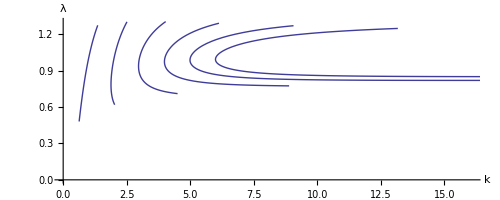

```mathematica
ParametricPlot[{Evaluate[{k[t],λ[t]}/.sol]},{t,-.5,.3},AxesLabel->{"k","λ"},AxesOrigin->{0,0}]
```

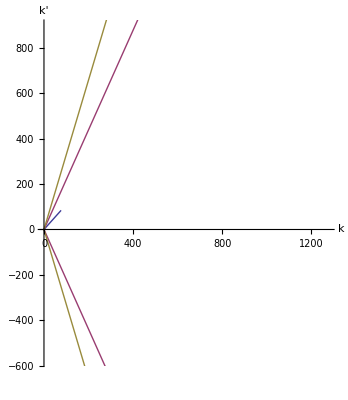

```mathematica
ParametricPlot[Evaluate[{k[t],k'[t]}/.sol],{t,-4,4},AxesLabel->{"k","k'"}]
```

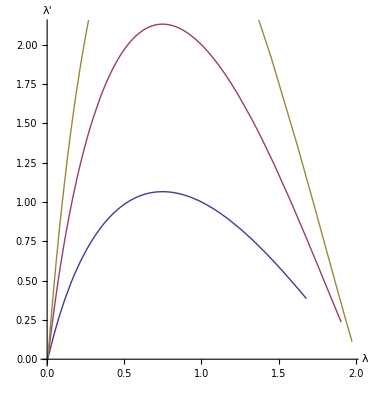

```mathematica
ParametricPlot[Evaluate[{λ[t],λ'[t]}/.sol],{t,-4,1},AxesLabel->{"λ","λ'"}]
```

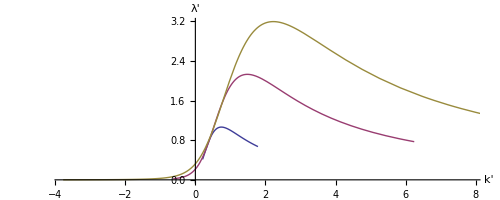

```mathematica
ParametricPlot[Evaluate[{k'[t],λ'[t]}/.sol],{t,-1,.5},AxesLabel->{"k'","λ'"}]
```